# EVRO SKOZI ČAS

## Pripravil: Arne Sven Sikošek, 2022/23

## PRIDOBIVANJE PODATKOV

Vse prikazane podatke sem dobil iz raznih spletnih strani. Vse povezave do teh spletnih strani bodo napisane spodaj.

```mathematica
Hyperlink["https://tradingeconomics.com/euro-area/inflation-cpi"]
```

https://tradingeconomics.com/euro-area/inflation-cpi

```mathematica
Hyperlink["https://ec.europa.eu/eurostat/statistics-explained/index.php?title=Exchange_rates_and_interest_rates"]
```

https://ec.europa.eu/eurostat/statistics-explained/index.php?title=Exchange_rates_and_interest_rates

```mathematica
Hyperlink["https://fred.stlouisfed.org/series/MYAGM2EZM196N"]
```

https://fred.stlouisfed.org/series/MYAGM2EZM196N

```mathematica
UporabnikiEvraSkoziCas = Import["C:\\faks programiranje\\ROM\\EvroSkoziČas.xlsx"][[1]];
```

```mathematica
EvroVGBP = Import["C:\\faks programiranje\\ROM\\EvroVGBP.xlsx"][[1]];

EvroVCHF = Import["C:\\faks programiranje\\ROM\\EvroVCHF.xlsx"][[1]];

EvroVUSD = Import["C:\\faks programiranje\\ROM\\EvroVUSD.xlsx"][[1]];
```

```mathematica
Drzave = Import["C:\\faks programiranje\\ROM\\DržaveVEvropi.xlsx", "Dataset", HeaderLines -> 1][[1]];
```

## UVOD

Evro je denarna enota, ki se uporablja večinoma znotraj Evropske Unije, vendar jo uporabljajo tudi v drugih državah v Evropi. Države, ki uporabljajo Evro rečemo, da so del t.i. “Evrocone” h kateri se je kot zadnja pridružila Hrvaška.

```mathematica
wiki = TextSentences[WikipediaData["Euro coins"]][[;;3]];
```

```mathematica
TextTranslation[wiki, #]&/@{"Slovenian"}
```

{{Obstaja osem apoenov eurokovancev, ki segajo od enega centa do dveh evrov (evro je razdeljen na sto centov).,Kovanci so se prvič začeli uporabljati leta 2002.,Imajo skupno hrbtno stran, ki prikazuje zemljevid Evrope, vendar ima vsaka država v evrskem območju svojo podobo na sprednji strani, kar pomeni, da ima vsak kovanec v obtoku naenkrat različne motive.}}

#### ZGODOVINA EVRA

```mathematica
zgodovina = TextSentences[WikipediaData["History of the euro"]][[;;3]];
TextTranslation[zgodovina, #]&/@{"Slovenian"}
```

{{Evro je nastal 1. januarja 1999, čeprav je bil cilj Evropske unije (EU) in njenih predhodnic že od leta 1960.,Po napornih pogajanjih je Maastrichtska pogodba začela veljati leta 1993, da bi do leta 1999 vzpostavila ekonomsko in monetarno unijo (EMU) za vse države EU, razen za Združeno kraljestvo in Dansko (čeprav ima Danska politiko fiksnega deviznega tečaja z evrom).,Valuta je bila oblikovana virtualno leta 1999; Bankovci in kovanci so začeli krožiti leta 2002.}}

## VREDNOST EVRA SKOZI ČAS

### MENJALNI TEČAJ EVRA IN BRITANSKEGA FUNTA

```mathematica
ListLinePlot[EvroVGBP]
```

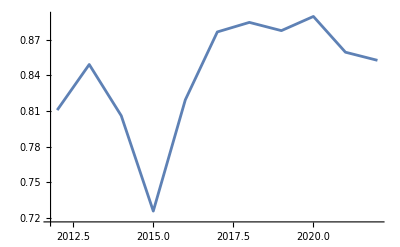

MENJALNI TEČAJ EVRA IN ŠVICARSKEGA FRANKA

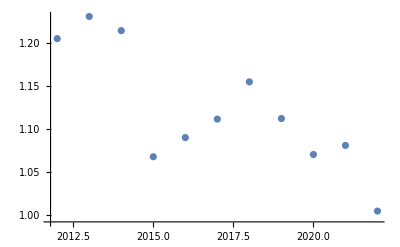

```mathematica
ListPlot[EvroVCHF]
```

## MENJALNI TEČAJ EVRA IN AMERIŠKEGA DOLARJA

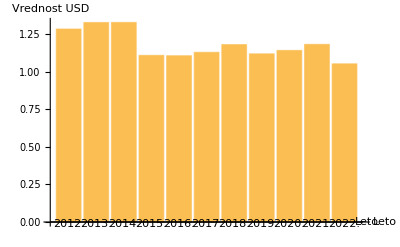

```mathematica
Leta=EvroVUSD[[2;;,1]];
VrednostUSD=EvroVUSD[[2;;,2]];
BarChart[VrednostUSD,ChartLabels->Leta,AxesLabel->{"Leto","Vrednost USD"}]
```

### UPORABNIKI EVRA ČEZ ČAS

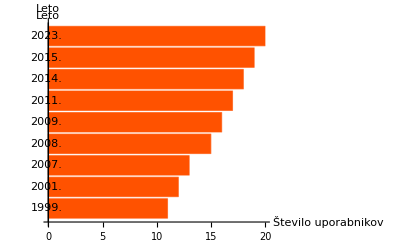

```mathematica
LetoPridruzitve= UporabnikiEvraSkoziCas[[2;;,1]];
stUporabnikov = UporabnikiEvraSkoziCas[[2;;,2]];
BarChart[stUporabnikov, ChartLabels ->LetoPridruzitve, AxesLabel ->{"Leto", Število uporabnikov}, BarOrigin->Left, ChartStyle -> "BlackBodySpectrum"]
```

### ZALOGA DENARJA V EVROPSKI UNIJI

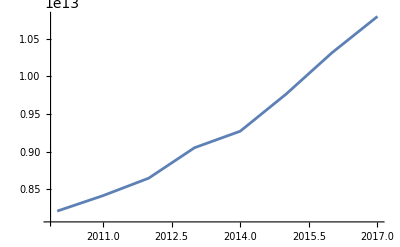

```mathematica
Zaloga =Import["C:\\faks programiranje\\ROM\\ZalogaEvra.xlsx", "Data"];
ListLinePlot[Zaloga]
```

### DRŽAVE V EVROPSKI UNIJI IN EVROCONI

```mathematica
EU= Select[Drzave, #[[2]]== "JA"&];
Evrocona = Select[Drzave, #[[3]]== "JA"&];
DrzaveVEU = EU[All, "Country"]// Normal;
GrafEU = Entity["Country", #]&/@DrzaveVEU;
DrzaveVEvroconi = Evrocona[All, "Country"] // Normal;
GrafEvrocone = Entity["Country",#]&/@DrzaveVEvroconi;
GeoListPlot[{GrafEU, GrafEvrocone}, GeoLabels -> Automatic, LabelStyle ->Directive[7,Italic,Black], PlotLegends -> {"Evropska Unija", "Evrocona"}]
```

## APLIKACIJA V OBLAKU

```mathematica
CloudDeploy[FormPage[<|"date"->"Date"|>,CurrencyConvert[Quantity[#quantity,DatedUnit["Euros",#date]],"Euros"]&],"url-path",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/as89208/url-path]